# Graviton Basis Toolkit: Mathematical Background, User Guide, Validation, and Worked Reduction Example

This report consolidates the mathematical setup, the software interface, the validation logic, and a nontrivial worked reduction example for graviton_basis_toolkit.wl. The emphasis is on connecting the abstract quotient constructions to the actual Mathematica computation.

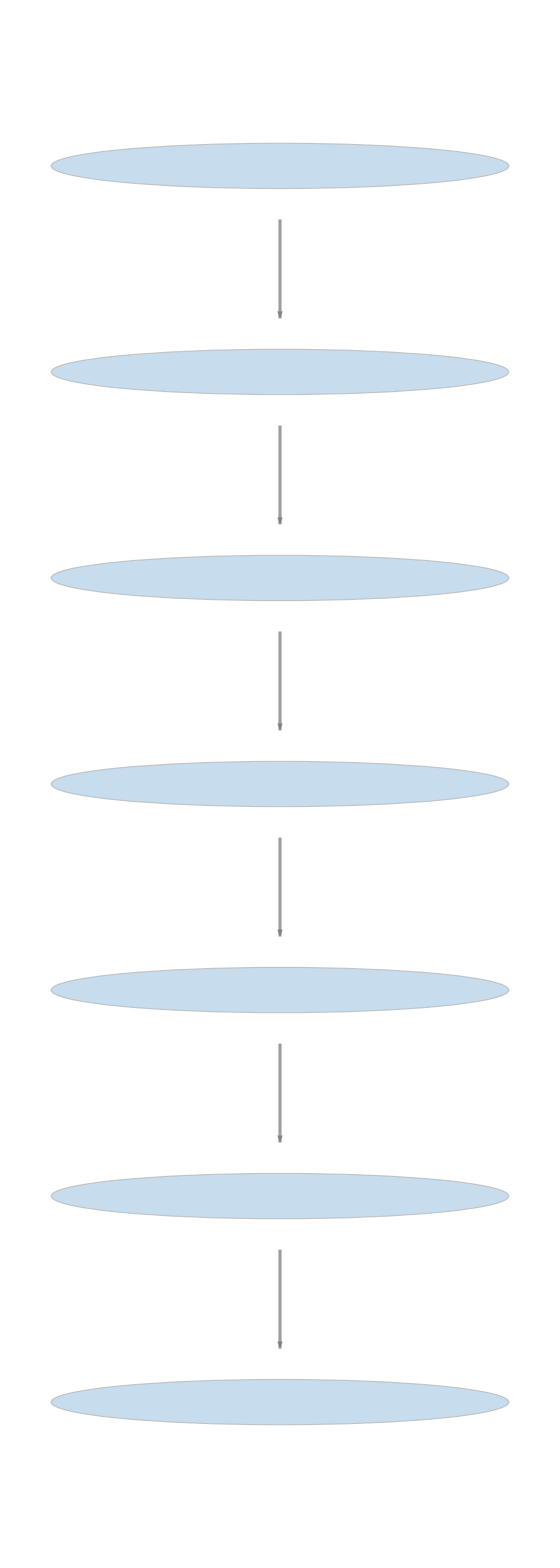

## 1. Mathematical Background

The toolkit works sector by sector. A sector is labeled by {nh, Nd}, where nh is the number of graviton fields h and Nd is the total number of derivatives. The starting point is the finite-dimensional vector space of local scalar operators in that sector.

Eq. (1)   V_(nh,Nd) := span of local scalar monomials built from nh gravitons and Nd derivatives.

The raw basis generated by the code is a concrete spanning set for V_(nh,Nd). It is obtained by distributing Nd derivatives among nh fields in all ordered ways, forming the corresponding derivative-decorated monomials, and then taking all scalar contractions.

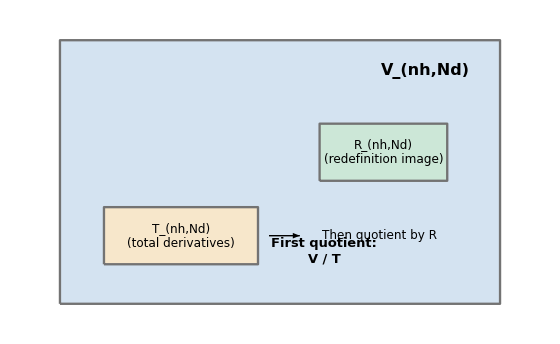

The first physical equivalence is integration by parts. Two Lagrangians define the same action if they differ by a total derivative.

Eq. (2)   L ~ L + d_mu K^mu.

Let T_(nh,Nd) denote the subspace of total derivatives inside V_(nh,Nd). The physically relevant space after IBP is the quotient V_(nh,Nd) / T_(nh,Nd).

Eq. (3)   Q_(nh,Nd) := V_(nh,Nd) / T_(nh,Nd).

The code identifies T_(nh,Nd) through the Euler-Lagrange operator. A local scalar density is a total derivative exactly when its Euler derivative vanishes.

Eq. (4)   L in T_(nh,Nd)  iff  delta L / delta h_(mu nu) = 0.

This is why IBPData constructs a generic linear combination of raw basis elements and solves VarD[h][L] == 0. The null space of that linear map is the space of IBP relations.

The second equivalence is field redefinition redundancy. For a local symmetric rank-2 tensor Delta h_(mu nu), the quadratic Fierz-Pauli Lagrangian changes by an equation-of-motion term plus a total derivative.

Eq. (5)   delta L_FP = E_FP^(mu nu) Delta h_(mu nu) + d_mu K^mu.

Therefore the image of the linear map Delta h -> E_FP^(mu nu) Delta h_(mu nu) is redundant inside the IBP quotient.

Eq. (6)   R_(nh,Nd) := Im(F_(nh-1,Nd-2 -> nh,Nd)) subset Q_(nh,Nd).

For interaction sectors, the final basis is the quotient of the IBP quotient by this image.

Eq. (7)   P_(nh,Nd) := Q_(nh,Nd) / R_(nh,Nd).

Quadratic sectors are intentionally treated differently. A linear field redefinition acts directly on the kinetic operator itself, so quotienting the quadratic sector by those directions is usually not the desired equivalence relation for the kinetic term.

Eq. (8)   nh < 3: use Q_(nh,Nd);   nh >= 3: use P_(nh,Nd).

The diagrams above summarize the two quotient operations: a kernel quotient for IBP and an image quotient for interaction-level field redefinitions.

## 2. User Guide and Code Reference

The normal workflow is: load the toolkit, compute sector data once with caching, inspect the basis of a sector if needed, and then reduce a Lagrangian either sector by sector or automatically.

Get["graviton_basis_toolkit.wl"]

res = RunBasisComputation[
  "MaxDimension" -> 5,
  "CacheDirectory" -> FileNameJoin[{Directory[], "basis_cache"}],
  "UseCache" -> True,
  "Verbose" -> True
];

red = ReduceLagrangian[lag,
  "CacheDirectory" -> FileNameJoin[{Directory[], "basis_cache"}],
  "UseCache" -> True
];

red["ReducedExpression"]

The public functions most users actually need are summarized below.

Function | Role
RunBasisComputation | Compute and cache sector data over a sector list.
ComputeSectorData | Assemble the raw basis, IBP quotient, redefinition image, and physical basis of one sector.
RawBasisOfSector | Return the raw scalar basis of a stored sector.
IBPBasisOfSector | Return the IBP quotient basis of a stored sector.
PhysicalBasisOfSector | Return the final basis after the interaction-sector field-redefinition quotient.
RedefinitionRulesOfSector | Return explicit independent field redefinitions and their images in the IBP basis.
ReduceSectorLagrangian | Reduce a known single-sector expression modulo IBP and field redefinitions.
ReduceLagrangian | Split a general expression by sector and reduce each sector automatically.

The small-sector summary below records the current behavior of the code in the sectors most relevant to the present report.

Sector | RawCount | IBPCount | RedefRank | PhysicalCount
{1,2} | 2 | 0 | 0 | 0
{2,2} | 10 | 4 | 0 | 4
{2,4} | 30 | 5 | 0 | 5
{3,2} | 28 | 14 | 4 | 10

The {2,2} and {2,4} quadratic sectors are shown after the current convention change that skips the field-redefinition quotient for nh < 3. The {3,2} sector is the first interaction sector and therefore exhibits a nontrivial redefinition image of rank 4.

## 3. Validation Report

The validation strategy is a direct implementation of Eq. (5). One chooses a generic Delta h_(mu nu), computes its Fierz-Pauli image, expands the resulting scalar Lagrangian, and then reduces it. Since the result lies in R_(nh,Nd), the reduced representative must vanish.

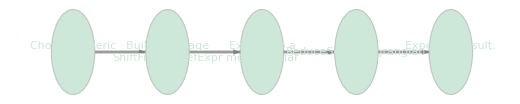

### 3.1 Detailed Validation in Sector {3,2}

For the first explicit validation, choose the coefficient vector {7, -11, 13, -17} in the independent redefinition basis of source sector {2,0}. The corresponding Delta h_(mu nu) is:

7*h[u, z$28894]*h[v, -z$28894]
- 11*h[u, v]*h[z$28894, -z$28894] +
  13*eta[u, v]*h[-z$28894, -z$28943]*h[z$28894, z$28943]
- 17*eta[u, v]*h[z$28894, -z$28894]*h[z$28943, -z$28943]

Its expanded Fierz-Pauli image in scalar sector {3,2} is:

11*h[a, b]*PD[-a][h[c, -c]]*PD[-b][h[z$28894, -z$28894]]
- 29*h[a, b]*PD[-b][h[z$28894, -z$28894]]*PD[-c][h[-a, c]]
- 7*h[a, b]*PD[-b][h[-a, c]]*PD[-c][h[z$28894, -z$28894]] +
  77*h[a, b]*PD[-c][h[z$28894, -z$28894]]*PD[c][h[-a, -b]]
- 90*h[a, -a]*PD[-c][h[z$28894, -z$28894]]*PD[c][h[b, -b]] +
  14*h[a, b]*PD[-c][h[-a, c]]*PD[-z$28894][h[-b, z$28894]] +
  14*h[a, b]*PD[-b][h[-a, c]]*PD[-z$28894][h[-c, z$28894]]
- 22*h[a, -a]*PD[-b][h[b, c]]*PD[-z$28894][h[-c, z$28894]]
- 66*h[a, b]*PD[c][h[-a, -b]]*PD[-z$28894][h[-c, z$28894]] +
  101*h[a, -a]*PD[c][h[b, -b]]*PD[-z$28894][h[-c, z$28894]]
- 14*h[a, b]*PD[-z$28894][h[-b, -c]]*PD[z$28894][h[-a, c]] +
  11*h[a, -a]*PD[-z$28894][h[-b, -c]]*PD[z$28894][h[b, c]]

This expression contains 12 explicit scalar terms after expansion. By Eq. (5), its class in P_(3,2) must vanish.

Object | Coordinates
Projected coordinates in the {3,2} IBP basis | {0,11,-36,77,-90,0,7,-66,101,14,14,-14,-29,11}
Recovered image coefficients | {7,-11,13,-17}
Physical coordinates after the quotient | {0,0,0,0,0,0,0,0,0,0}

The recovered image coefficients match the chosen field-redefinition coefficients exactly, and the physical coordinates are all zero. The reduced expression returned by the toolkit is:

0

This is the computational realization of Eq. (6): the entire expression lies inside the redefinition image R_(3,2).

### 3.2 Stored Stress Test in Sector {3,4}

The second validation is the stronger one. It uses all 33 independent redefinition-basis directions of source sector {2,2}, producing a 240-term scalar Lagrangian in target sector {3,4}. The reducer again returns zero.

Sector | IBPCount | RedefRank | PhysicalCount | DeltaBasisLength | LagTermCount | Reduced to 0?
{3,2} | 14 | 4 | 10 | 4 | 18 | True
{3,4} | 64 | 33 | 31 | 33 | 240 | True

The {3,4} test is important because it shows that the image quotient is working in a genuinely large sector, not only in a small toy example.

## 4. Worked Example: A Nontrivial Lagrangian Reduction

To show a nonzero outcome, consider a sector-{3,2} Lagrangian built from three pieces: one physical contribution, one explicit IBP-trivial contribution, and one explicit field-redefinition image.

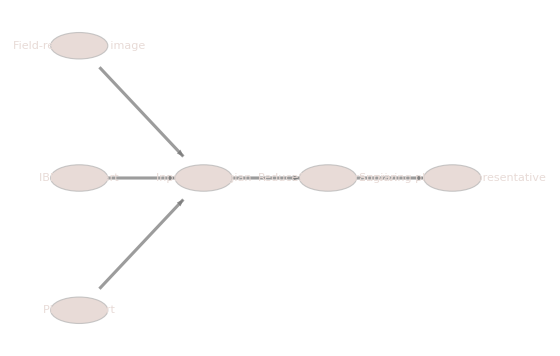

Eq. (9)   L_in = L_phys + 4 L_IBP + L_redef.

The physical part is chosen directly in the stored physical basis with target coordinate vector {2, -3, 0, ..., 0}.

2*h[a, b]*PD[-a][h[c, d]]*PD[-b][h[-c, -d]]
- 3*h[a, b]*PD[-b][h[-a, c]]*PD[-d][h[-c, d]]

The IBP-trivial contribution is chosen from the stored relation expressions, so by Eq. (4) it is a total derivative:

h[a, b]*PD[-b][h[d, -d]]*PD[-c][h[-a, c]] +
  h[a, b]*PD[-b][h[-a, c]]*PD[-c][h[d, -d]] +
  h[-a, c]*h[a, b]*PD[-c][PD[-b][h[d, -d]]]

The field-redefinition contribution is chosen from the image of the Fierz-Pauli variation using image coefficients {5, -7, 11, -13}:

7*h[a, b]*PD[-a][h[c, -c]]*PD[-b][h[z$28894, -z$28894]]
- 19*h[a, b]*PD[-b][h[z$28894, -z$28894]]*PD[-c][h[-a, c]]
- 5*h[a, b]*PD[-b][h[-a, c]]*PD[-c][h[z$28894, -z$28894]] +
  61*h[a, b]*PD[-c][h[z$28894, -z$28894]]*PD[c][h[-a, -b]]
- 66*h[a, -a]*PD[-c][h[z$28894, -z$28894]]*PD[c][h[b, -b]] +
  10*h[a, b]*PD[-c][h[-a, c]]*PD[-z$28894][h[-b, z$28894]] +
  10*h[a, b]*PD[-b][h[-a, c]]*PD[-z$28894][h[-c, z$28894]]
- 14*h[a, -a]*PD[-b][h[b, c]]*PD[-z$28894][h[-c, z$28894]]
- 54*h[a, b]*PD[c][h[-a, -b]]*PD[-z$28894][h[-c, z$28894]] +
  73*h[a, -a]*PD[c][h[b, -b]]*PD[-z$28894][h[-c, z$28894]]
- 10*h[a, b]*PD[-z$28894][h[-b, -c]]*PD[z$28894][h[-a, c]] +
  7*h[a, -a]*PD[-z$28894][h[-b, -c]]*PD[z$28894][h[b, c]]

Combining the three pieces gives the following input Lagrangian:

2*h[a, b]*PD[-a][h[c, d]]*PD[-b][h[-c, -d]] +
  7*h[a, b]*PD[-a][h[c, -c]]*PD[-b][h[d, -d]]
- 15*h[a, b]*PD[-b][h[d, -d]]*PD[-c][h[-a, c]]
- h[a, b]*PD[-b][h[-a, c]]*PD[-c][h[d, -d]] +
  4*h[-a, c]*h[a, b]*PD[-c][PD[-b][h[d, -d]]] +
  61*h[a, b]*PD[-c][h[d, -d]]*PD[c][h[-a, -b]]
- 66*h[a, -a]*PD[-c][h[d, -d]]*PD[c][h[b, -b]] +
  10*h[a, b]*PD[-c][h[-a, c]]*PD[-d][h[-b, d]] +
  7*h[a, b]*PD[-b][h[-a, c]]*PD[-d][h[-c, d]]
- 14*h[a, -a]*PD[-b][h[b, c]]*PD[-d][h[-c, d]]
- 54*h[a, b]*PD[c][h[-a, -b]]*PD[-d][h[-c, d]] +
  73*h[a, -a]*PD[c][h[b, -b]]*PD[-d][h[-c, d]]
- 10*h[a, b]*PD[-d][h[-b, -c]]*PD[d][h[-a, c]] +
  7*h[a, -a]*PD[-d][h[-b, -c]]*PD[d][h[b, c]]

This input contains 14 explicit terms after expansion. The mathematical prediction from Eqs. (4), (5), and (9) is immediate:

Eq. (10)   [L_in] = [L_phys] + 4[0] + [0] = [L_phys].

The actual Mathematica computation reproduces exactly that logic. First the full input is projected into the {3,2} IBP basis; then the field-redefinition image component is subtracted.

Object | Coordinates
Projected coordinates in the {3,2} IBP basis | {2,7,-24,61,-66,-3,5,-54,73,10,10,-10,-19,7}
Coordinates after subtracting the image | {2,0,0,0,0,-3,0,0,0,0,0,0,0,0}
Final physical coordinates | {2,-3,0,0,0,0,0,0,0,0}
Recovered image coefficients | {5,-7,11,-13}

The final physical coordinates are exactly {2, -3, 0, ..., 0}, which is the coordinate vector of the chosen physical part. The surviving reduced expression is:

2*h[a, b]*PD[-a][h[c, d]]*PD[-b][h[-c, -d]]
- 3*h[a, b]*PD[-b][h[-a, c]]*PD[-d][h[-c, d]]

The equality of the reduced expression and the chosen physical part is checked explicitly in the data file and evaluates to True.

### 4.1 Mathematica Commands for the Worked Example

sec = ComputeSectorData[3, 2, Sequence @@ opts];
physCoeffs = ReplacePart[ConstantArray[0, sec["PhysicalCount"]], {1 -> 2, 2 -> -3}];
physExpr = canonExpr @ LinearCombination[physCoeffs, sec["PhysicalBasis"]];
ibpExpr = sec["IBPRelationExpressions"][[1]];
redefCoeffs = {5, -7, 11, -13};
redefExpr = canonExpr @ Total[MapThread[Times, {redefCoeffs, sec["RedefShiftImages"]}]];
lag = canonExpr @ Expand[physExpr + 4 ibpExpr + redefExpr];
red = ReduceSectorLagrangian[lag, 3, 2, Sequence @@ opts];

This is the simplest nontrivial example I know of that shows both kinds of redundancy being removed while leaving a nonzero physical answer.

## 5. Reproduction and Auxiliary Files

The report itself was generated from the current code and the current stored validation output. The main auxiliary files are:

graviton_basis_toolkit_validation.wls and graviton_basis_toolkit_validation_output.wl for the stored redundancy tests.

build_graviton_basis_docs.wls for the smaller notebook/PDF documentation set.

build_graviton_basis_toolkit_comprehensive_report.wls for this combined report.

graviton_basis_toolkit_comprehensive_report_data.wl for the machine-readable data shown in this report.

If the implementation changes, rerun the validation script first and then rerun the comprehensive report build script so that the report stays synchronized with the code.

End of report.